## Figure 6

```mathematica
path=NotebookDirectory[];
```

```mathematica
options={DataRange->{1,100},Joined->True,Mesh->All,PlotStyle->{Directive[Red,Opacity[0.15]],Directive[Red,Opacity[0.30]],Directive[Red,Opacity[0.45]],Directive[Red,Opacity[0.60]],Directive[Red,Opacity[0.75]],Directive[Red,Opacity[0.9]]},Frame->True,PlotRange->{Automatic,{-0.05,1.05}},MeshStyle->Directive[PointSize[0.02]],FrameLabel->{Style["Number of released DD",Black,16],Style["Fixation probability of DD",Black,16]},FrameStyle->Directive[Black,Thickness[0.003]],PlotLegends->Placed[{"k = 4","k = 8","k = 16","k = 32"},{0.8,Center}]};
```

### For the cost of gene drive c = 0.0

```mathematica
c0k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
c0k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
c0k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
c0k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

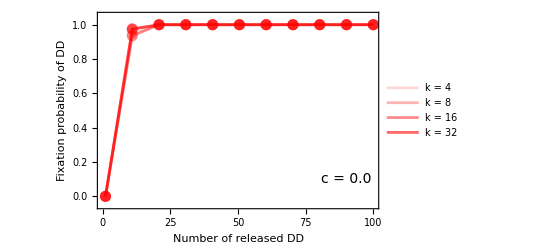

```mathematica
p0=ListPlot[{Rescale[c0k4⟦All,2⟧],Rescale[c0k8⟦All,2⟧],Rescale[c0k16⟦All,2⟧],Rescale[c0k32⟦All,2⟧]}//N,options,Epilog->Inset[Style["c = 0.0",14,Black],{90,0.1}]]
```

### For the cost of gene drive c = 0.1

```mathematica
c1k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.1_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
c1k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.1_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
c1k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.1_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
c1k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.1_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

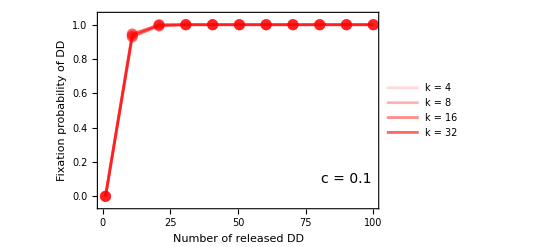

```mathematica
p1=ListPlot[{Rescale[c1k4⟦All,2⟧],Rescale[c1k8⟦All,2⟧],Rescale[c1k16⟦All,2⟧],Rescale[c1k32⟦All,2⟧]}//N,Epilog->Inset[Style["c = 0.1",14,Black],{90,0.1}],options]
```

### For the cost of gene drive c = 0.2

```mathematica
c2k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.2_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
c2k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.2_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
c2k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.2_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
c2k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.2_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

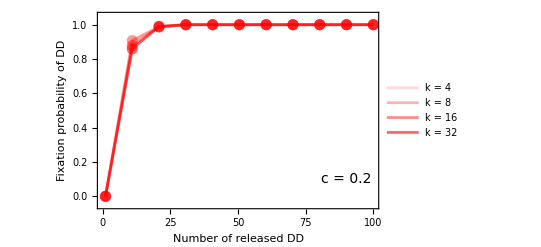

```mathematica
p2=ListPlot[{Rescale[c2k4⟦All,2⟧],Rescale[c2k8⟦All,2⟧],Rescale[c2k16⟦All,2⟧],Rescale[c2k32⟦All,2⟧]}//N,Epilog->Inset[Style["c = 0.2",14,Black],{90,0.1}],options]
```

### For the cost of gene drive c = 0.3

```mathematica
c3k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.3_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
c3k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.3_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
c3k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.3_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
c3k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.3_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

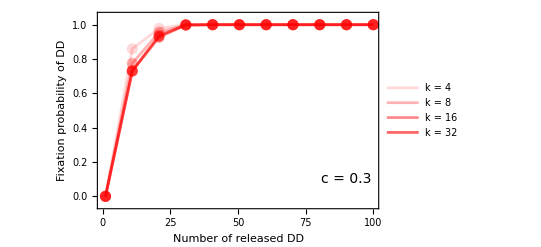

```mathematica
p3=ListPlot[{Rescale[c3k4⟦All,2⟧],Rescale[c3k8⟦All,2⟧],Rescale[c3k16⟦All,2⟧],Rescale[c3k32⟦All,2⟧]}//N,Epilog->Inset[Style["c = 0.3",14,Black],{90,0.1}],options]
```

### For the cost of gene drive c = 0.4

```mathematica
c4k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.4_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
c4k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.4_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
c4k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.4_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
c4k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.4_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

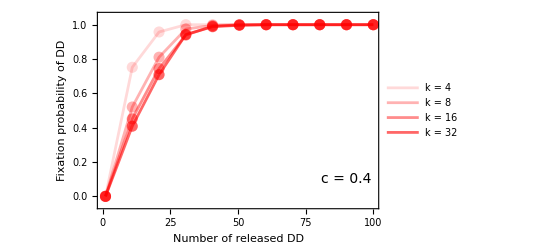

```mathematica
p4=ListPlot[{Rescale[c4k4⟦All,2⟧],Rescale[c4k8⟦All,2⟧],Rescale[c4k16⟦All,2⟧],Rescale[c4k32⟦All,2⟧]}//N,Epilog->Inset[Style["c = 0.4",14,Black],{90,0.1}],options]
```

### For the cost of gene drive c = 0.5

```mathematica
k4=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.5_n_100_vary_theta_trail_1000_k_4.txt","CSV"];
k8=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.5_n_100_vary_theta_trail_1000_k_8.txt","CSV"];
k16=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.5_n_100_vary_theta_trail_1000_k_16.txt","CSV"];
k32=Import[path<>"/fixation_prob_rand_1_p_0.95_c_0.5_n_100_vary_theta_trail_1000_k_32.txt","CSV"];
```

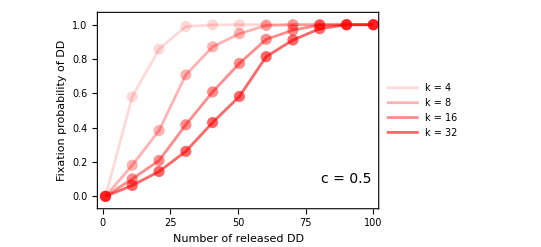

```mathematica
p5=ListPlot[{Rescale[k4⟦All,2⟧],Rescale[k8⟦All,2⟧],Rescale[k16⟦All,2⟧],Rescale[k32⟦All,2⟧]}//N,Epilog->Inset[Style["c = 0.5",14,Black],{90,0.1}],options]
```

### All collated

```mathematica
Manipulate[{p0,p1,p2,p3,p4,p5}⟦i⟧,{i,1,6,1}]
```

```mathematica
For[i=1,i≤6,i++,
Export["/Users/gokhale/Desktop/"<>"image"<>ToString[i]<>".pdf",{p0,p1,p2,p3,p4,p5}⟦i⟧]
]
```

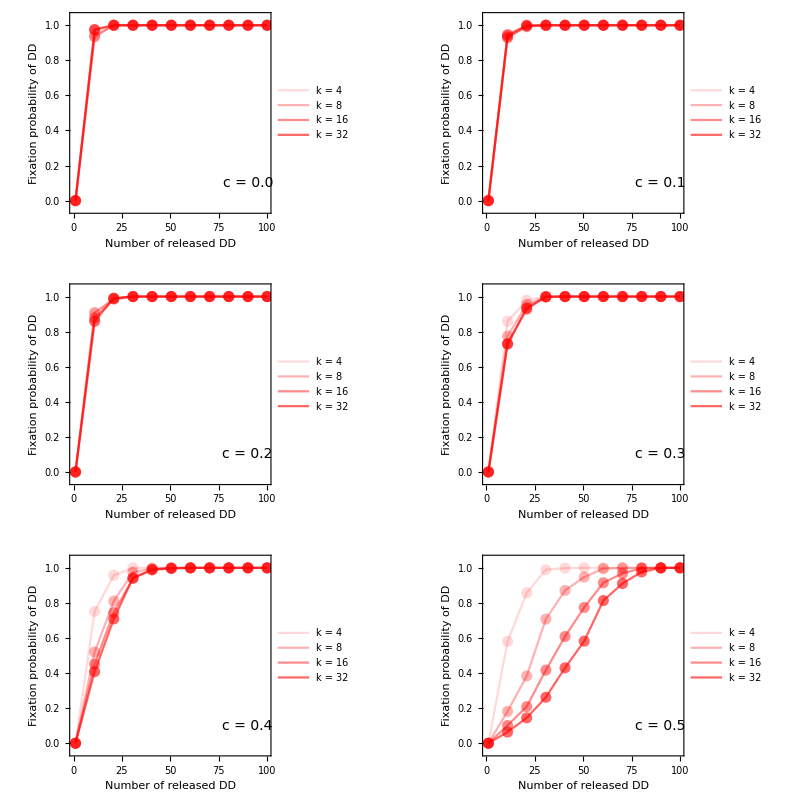

```mathematica
GraphicsGrid[Partition[{p0,p1,p2,p3,p4,p5},2]]
```

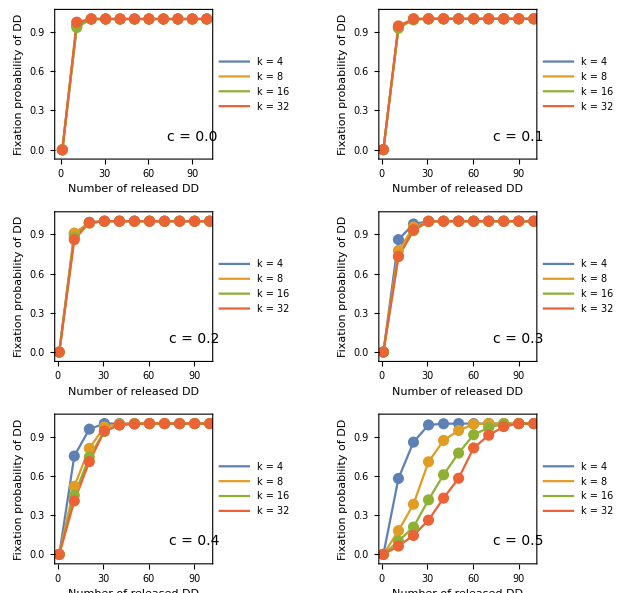

```mathematica
Export[path<>"explorecosts.gif",{p0,p1,p2,p3,p4,p5},FrameRate->10]
```

/Users/gokhale/Documents/Working/BfN/genedrives_mating_GitHub/genedrives_mating/FigureB2/code&data/explorecosts.gif

```mathematica
Export[path<>"explorecosts.gif",ListAnimate[{p0,p1,p2,p3,p4,p5},AnimationRate->1]]
```

/Users/gokhale/Documents/Working/BfN/genedrives_mating_GitHub/genedrives_mating/FigureB2/code&data/explorecosts.gif